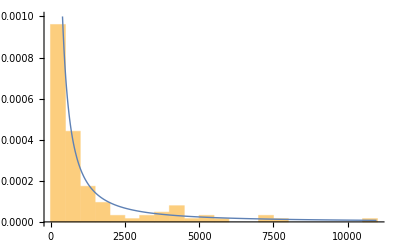

```mathematica
Clear["Global`*"];

sample={1209,1201,25,1150,1826,3550,975,23,906,1587,7303,736,106,625,4027,1078,264,164,3530,832,196,675,363,5436,791,446,171,582,3080,758,202,96,504,2410,688,587,65,488,1303,7297,588,957,1053,1656,580,93,383,3005,1264,630,78,327,5483,1536,125,469,1600,4482,677,763,619,1298,881,373,71,702,828,86,368,2681,1322,236,193,4766,951,128,293,366,4162,307,69,257,691,2434,232,51,234,129,1088,85,29,131,138,1520,610,57,189,7970,177,125,50,267,3734,4,11,51,51,184,749,12,7,20,134,4444,15,22,90,4235,71,662,928,1186,10968,6,17,13,5845};

edist1=ParetoDistribution[280,0.4786874918577795];

Show[Histogram[sample,30,"PDF",PlotRange->All],Plot[{PDF[edist1,x]},{x,Min[sample],Max[sample]},PlotStyle->Thick,PlotRange->{{1,10000},{0.000001,0.001}}]
]
```

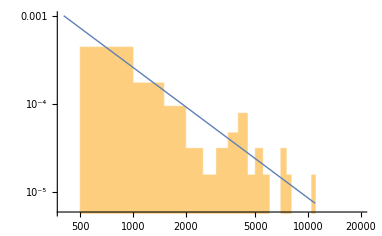

```mathematica
Show[Histogram[sample,30,"PDF",ScalingFunctions->{"Log","Log"},PlotRange->{{400,20000},{0.000006,0.001}}],LogLogPlot[{PDF[edist1,x]},{x,Min[sample],Max[sample]},PlotStyle->Thick,PlotRange->{{400,20000},{0.000006,0.001}}]
]
```